## Actividad 02

```mathematica
imagenDistancia=Import["C:\\Users\\FatalRaincloud\\Downloads\\la foto 1 (3).JPG"]
```

-Graphics-

```mathematica
pixels={{563.406,993.577},{2445.6,1102.09}}
```

{{563.406,993.577},{2445.6,1102.09}}

```mathematica
x1=pixels[[1,1]]
```

563.406

```mathematica
x2=pixels[[2,1]]
```

2445.6

```mathematica
y1=pixels[[1,2]]
```

993.577

```mathematica
y2=pixels[[2,2]]
```

1102.09

```mathematica
distancia=Sqrt[(x2-x1)^2+(y2-y1)^2]
```

1885.32

```mathematica
imagenFuncion=Import["C:\\Users\\FatalRaincloud\\Downloads\\la foto 2 (1).JPG"]
```

-Graphics-

```mathematica
datos={{834.676,1291.97},{884.756,1308.67},{916.057,1337.88},{953.617,1415.09},{970.311,1523.6},{1003.7,1607.06},{1035.,1652.97},{1097.6,1694.71},{1164.37,1711.4},{1247.84,1713.49},{1322.96,1698.88},{1385.56,1673.84},{1427.3,1634.19},{1485.72,1506.9},{1460.68,1565.33},{1525.37,1452.65},{1579.62,1415.09},{1673.53,1415.09},{1744.47,1431.78},{1819.59,1450.56},{1907.23,1477.69},{1976.1,1519.42},{2017.83,1573.68},{2038.7,1642.54}};
```

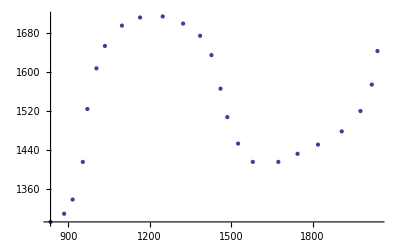

```mathematica
ListPlot[datos]
```

```mathematica
Clear[a,b,c,d,a1,b1,c1,d1]
```

d1+a1 Cos[c1+e+(b1 π x)/90]

{a→1.,b→1.,c→1.,d→1.,a1→-197.611,b1→0.18948,c1→-3445.17,d1→1539.55,e→3502.91}

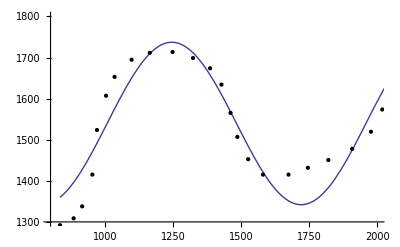

```mathematica
modelo=a*Sin[b*x*((4Pi)/90)+c]+d+a1 Cos[b1 x*(Pi/180)+c1]+d1;
modelo=a1 Cos[b1 x*((2Pi)/180)+c1+e]+d1
regresion =FindFit[datos,modelo,{a,b,c,d,a1,b1,c1,d1,e},x]
regreF = Function[{}, Evaluate[modelo/.regresion]];
Plot[regreF[x], {x, 835, 2038}, PlotRange->{{800, 2000}, {1300, 1800}}, Epilog->Map[Point, datos]]
```

```mathematica
g=Interpolation[datos]
```

InterpolatingFunction[{{834.676,2038.7}},<>]

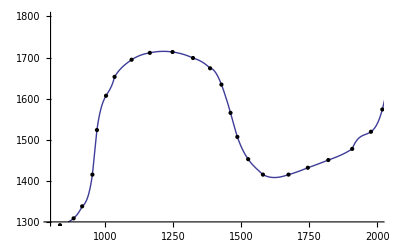

```mathematica
Plot[g[x], {x, 835, 2038}, PlotRange->{{800, 2000}, {1300, 1800}}, Epilog->Map[Point, datos]]
```

```mathematica
D[g[x],x]
```

InterpolatingFunction[{{834.676,2038.7}},<>][x]

```mathematica
Clear[a1,a2,a3,a4,a5,a6,a7]
```

a6+a5 x+a4 x^2+a3 x^3

{a3→3.12718×10^-6,a4→-0.0139519,a5→19.9596,a6→-7561.22}

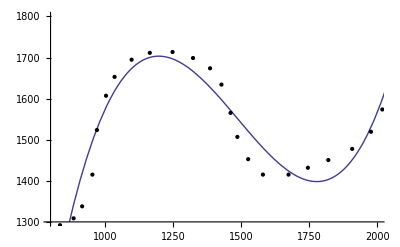

```mathematica
modelo=a*Sin[b*x*((4Pi)/90)+c]+d+a1 Cos[b1 x*(Pi/180)+c1]+d1;
modelo=a3 x^3+a4 x^2+a5 x+a6+a2 x^4+
regresion =FindFit[datos,modelo,{a3,a4,a5,a6},x]
regreF = Function[{}, Evaluate[modelo/.regresion]];
Plot[regreF[x], {x, 835, 2038}, PlotRange->{{800, 2000}, {1300, 1800}}, Epilog->Map[Point, datos]]
```

```mathematica
D[funcion[y],y]
```

19.9596-0.0279039 y+9.38155×10^-6 y^2

```mathematica
funcion[y_]:=regreF[[2]]/.x->y;
```

```mathematica
funcion[1]
```

-7541.28

```mathematica
der[y_]:=19.959627883278316-0.02790386905970265 y+9.381545067130393*^-6 y^2
```

```mathematica
der[0]
```

19.9596

```mathematica
finalFunction[x_]:=Sqrt[1+(der[x])^2]
```

```mathematica
finalFunction[0]
```

19.9847

```mathematica
metodoSimpson[a0_,b0_,n0_]:=Module[{a=N[a0],b=N[b0],n=n0,i},
h=(b-a)/(2*n);
sumPar = 0;
For[i=1,i≤ n-1,i++,
sumPar =sumPar+finalFunction[a+i*h*2];];
sumImpar = 0;
For[i=1,i≤ n,i++,
sumImpar =sumImpar+finalFunction[a+h*(2*i-1)];];
Return[h/3(finalFunction[a]+finalFunction[b]+2*sumPar+4*sumImpar)];
];
```

```mathematica
NIntegrate[finalFunction[x],{x,834.676,2038.7}]
```

1701.22

## Analizando Errores

```mathematica
regreF
```

Function[{},31420.4-129.719 x+0.210327 x^2-0.000160858 x^3+5.85656×10^-8 x^4-8.18414×10^-12 x^5]

```mathematica
g1[y_]:=regreF[[2]]
```

```mathematica
TableForm[
Table[{i,datos[[i,2]],funcion[datos[[i,1]]],
Abs[(datos[[i,2]]-funcion[datos[[i,1]]])/datos[[i,2]]*100]},{i,1,Length[datos]}],TableHeadings->{None,{"Iteración","Valor Real","Aproximacióm","Error"}}]
```

Iteración | Valor Real | Aproximacióm | Error
1 | 1291.97 | 1196.98 | 7.35196
2 | 1308.67 | 1342.53 | 2.58714
3 | 1337.88 | 1418.95 | 6.05944
4 | 1415.09 | 1496.84 | 5.77724
5 | 1523.6 | 1526.87 | 0.214746
6 | 1607.06 | 1578.91 | 1.75165
7 | 1652.97 | 1618.5 | 2.08562
8 | 1694.71 | 1673.31 | 1.26298
9 | 1711.4 | 1700.31 | 0.647956
10 | 1713.49 | 1696.75 | 0.977088
11 | 1698.88 | 1666.48 | 1.90706
12 | 1673.84 | 1627.64 | 2.76008
13 | 1634.19 | 1597.31 | 2.25696
14 | 1506.9 | 1551.87 | 2.9843
15 | 1565.33 | 1571.57 | 0.398955
16 | 1452.65 | 1520.75 | 4.68807
17 | 1415.09 | 1480.23 | 4.60335
18 | 1415.09 | 1423.88 | 0.621384
19 | 1431.78 | 1400.92 | 2.15512
20 | 1450.56 | 1403.24 | 3.26222
21 | 1477.69 | 1450.99 | 1.8072
22 | 1519.42 | 1530.35 | 0.719357
23 | 1573.68 | 1599.22 | 1.6228
24 | 1642.54 | 1640.08 | 0.149852

```mathematica
a=834.676
b=2038.7
```

834.676

2038.7

```mathematica
metodoSimpson[a,b,15]
```

1701.22

```mathematica
(** Distancia Real = 1885.32 **)
```